```mathematica
Integrate[Exp[-β (m ω q^2)/2],{q,-Infinity,Infinity}]
```

ConditionalExpression[(√(2 π))/(√(m β ω)), Re[m β ω]>0]

```mathematica
Dt[r'[t]^2]
```

2 Dt[t] r'[t] r''[t]

```mathematica
Limit[3n kb (Te/T)^2 Exp[-Te/T]/(1-Exp[-Te/T])^2,T->0]
```

(3 ⅇ^(-Te/0^+) kb n Te^2)/((1-ⅇ^(-Te/0^+))^2 (0^+)^2)

```mathematica
Expand[(1-Exp[-Te/T])^2]
```

1+ⅇ^(-(2 Te)/T)-2 ⅇ^(-Te/T)

```mathematica
Series[3n kb (Te/T)^2 Exp[-Te/T]/(1-Exp[-Te/T])^2,{T,0,1}]
```

(ⅇ^(-Te/T+O[T]^2) ((3 kb n Te^2)/T^2+O[T]^2))/((-1+ⅇ^(-Te/T+O[T]^2))^2)

```mathematica
Limit[1/(1-Exp[-1/T])^2,T->x]
```

1/((1-ⅇ^(-1/x))^2)

```mathematica
img1=Plot[1/(1-Exp[-1/T])^2,{T,-1,1},AxesLabel->{"T/T_E","1/(1 - SuperscriptBox[ⅇ, -SubscriptBox[T, E]/T])^2"},Ticks->None,LabelStyle->Directive[Bold, Medium],PlotStyle->Red];
```

```mathematica
Export["/home/mcard/school/FA22/PHYS163a/figs/exponential.png",img1]
```

/home/mcard/school/FA22/PHYS163a/figs/exponential.png

```mathematica
lim_(T->0^+) Exp[1/T]
```

∞

```mathematica
1/E^(-1/T)
```

ⅇ^(1/T)

```mathematica
Exp[-1/t]/Exp[-1/t]^2
```

ⅇ^(1/t)

```mathematica
(Sinh[x]+Cosh[x])//TrigToExp
```

ⅇ^x

```mathematica
{{1,0},{0,-1}}.{{Exp[μ β B],0},{0,Exp[-μ β B]}}//MatrixForm
{{0,1},{1,0}}.{{1,Tanh[μ β B]},{Tanh[μ β B],1}}//MatrixForm
```

(ⅇ^(B β μ) | 0
0 | -ⅇ^(-B β μ))

(Tanh[B β μ] | 1
1 | Tanh[B β μ])

```mathematica
D[ρ[t] Log[ρ[t]],t]
```

ρ'[t]+Log[ρ[t]] ρ'[t]

```mathematica
MatrixLog[{{2,0},{0,2}}]
```

{{Log[2],0},{0,Log[2]}}

```mathematica
S[n_]:=(4n+1)Exp[-(β ℏ^2)/i n(2n+1)]
```

```mathematica
Table[S[n],{n,0,1}]
```

{1,5 ⅇ^(-(3 β ℏ^2)/i)}

```mathematica
Limit[S[n],n->∞]
```

ConditionalExpression[0, i β ℏ^2>0]

```mathematica
Sum[S[n],{n,0,Infinity}]
```

∑_(n=0)^∞ ⅇ^(-(n (1+2 n) β ℏ^2)/i) (1+4 n)

```mathematica
Sum[Exp[-2(√(β/i)ℏ n)^2]4(√(β/i)ℏ n)(√(β/i)ℏ),{n,0,Infinity}]
```

∑_(n=0)^∞ (4 ⅇ^(-(2 n^2 β ℏ^2)/i) n β ℏ^2)/i

```mathematica
Integrate[4x Exp[-2 x^2],{x,0,Infinity}]
```

1

```mathematica
S[n_]:=3(4n+3)Exp[-(β ℏ^2)/i(2n+1)(n+1)]
```

```mathematica
S[0]
```

9 ⅇ^(-(β ℏ^2)/i)

```mathematica
Simplify[21 ⅇ^(-(6 β ℏ^2)/i)+9 ⅇ^(-(β ℏ^2)/i)]
```

3 ⅇ^(-(6 β ℏ^2)/i) (7+3 ⅇ^((5 β ℏ^2)/i))

```mathematica
n=10;
Sum[1/(n!(n-m)!),{m,1,n}]
```

98641/131681894400

```mathematica
D[Log[1+9Exp[-β ℏ^2/i]],β]
```

-(9 ⅇ^(-(β ℏ^2)/i) ℏ^2)/((1+9 ⅇ^(-(β ℏ^2)/i)) i)

```mathematica
Simplify[-(9 ⅇ^(-(β ℏ^2)/i) ℏ^2)/((1+9 ⅇ^(-(β ℏ^2)/i)) i)]
```

-(9 ℏ^2)/(9 i+ⅇ^((β ℏ^2)/i) i)

```mathematica
Gamma[5/2]
```

(3 √π)/4

```mathematica
-D[Log[1/(1-Exp[-x])],x]
```

ⅇ^-x/(1-ⅇ^-x)

```mathematica
Integrate[(ℏ c k)/(Exp[β ℏ c k]-1)k^2,{k,0,Infinity}]
```

ConditionalExpression[π^4/(15 c^3 β^4 ℏ^3), Re[c β ℏ]>0]

```mathematica
π^4/(15 c^3 β^4 ℏ^3)(4π V)/(2π)^3
```

(π^2 V)/(30 c^3 β^4 ℏ^3)

```mathematica
Integrate[k^2 Log[1-Exp[-β ℏ c k]],{k,0,Infinity}]
```

ConditionalExpression[-π^4/(45 c^3 β^3 ℏ^3), Re[c β ℏ]>0]

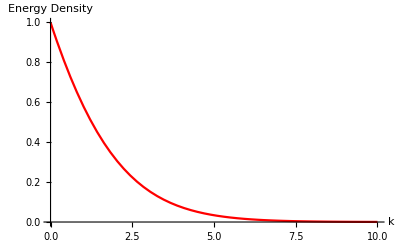

/home/mcard/school/FA22/PHYS163a/figs/energydensity.png

```mathematica
img2=Plot[Abs[k]/(Exp[Abs[k]]-1),{k,0,10},AxesLabel->{"k","Energy Density"},Ticks->None,LabelStyle->Directive[Bold, Medium],PlotStyle->Red]
Export["/home/mcard/school/FA22/PHYS163a/figs/energydensity.png",img2]
```

```mathematica
Series[k/(Exp[k]-1),{k,0,1}]
```

1-k/2+O[k]^2

```mathematica
D[Log[z[β]],β]
```

z'[β]/z[β]

```mathematica
-D[Log[((2π)/β)^(3M)],β]
```

-(3 M)/β